/Users/chipdelmal/Desktop

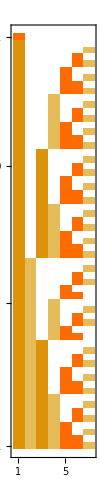
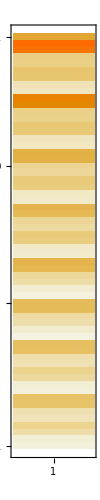
-Graphics- | -Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
data=Import["gamEIR1.csv"];
Grid[{{
(Transpose[data[[2;;All]]][[1;;7]])//MatrixPlot[#//Transpose,ImageSize->{100,500}]&,
(Transpose[data[[2;;All]]][[8]])//MatrixPlot[{#}//Transpose,ImageSize->{100,500},PlotLegends->Automatic]&
}}]
```